```mathematica
A = {{-17/36, -7/18, -7/18}, {17/72, 25/36, 43/36}, {-55/72, -11/36, 7/36}};
B = {{2/3}, {-1/3}, {-1/3}};
C1 = {{0, 1, -1}};
```

#### Punto 6

```mathematica
G[z_]:= (Simplify[C1.Inverse[z IdentityMatrix[3] - A].B])[[1,1]]
```

```mathematica
G[z]
```

-24/(1-3 z-10 z^2+24 z^3)

```mathematica
numz = Expand[Numerator[G[z]]]
```

-24

```mathematica
denz = Expand[Denominator[G[z]]]
```

1-3 z-10 z^2+24 z^3

```mathematica
Subscript[G, armz][z_]:=numz/denz
```

```mathematica
Subscript[G, armz][z]
```

-24/(1-3 z-10 z^2+24 z^3)

```mathematica
Armaz = Expand[Denominator[Subscript[G, armz][z]]Y[z]== Numerator[Subscript[G, armz][z]]Subscript[U, 1][z]]
```

Y[z]-3 z Y[z]-10 z^2 Y[z]+24 z^3 Y[z]==-24 U_1[z]

Porto nel dominio di k

```mathematica
Armak =Armaz /. {Y[z]->y[k],z Y[z]->y[k + 1],z^2 Y[z]->y[k + 2],z^3 Y[z]->y[k + 3], Subscript[U, 1][z]->Subscript[u, 1][k]}
```

y[k]-3 y[1+k]-10 y[2+k]+24 y[3+k]==-24 u_1[k]

Scrivo le condizioni iniziali

```mathematica
Subscript[x, 10]={{-3},{-1},{1}}
```

{{-3},{-1},{1}}

```mathematica
Subscript[x, 10]//MatrixForm
```

(-3
-1
1)

Calcolo y[0],y[1],y[2]

```mathematica
Subscript[y, 100]= (C1.Subscript[x, 10])[[1,1]]
```

-2

```mathematica
Subscript[y, 101]= (C1.A.Subscript[x, 10])[[1,1]]
```

-3

```mathematica
Subscript[y, 102]= (C1.A.A.Subscript[x, 10])[[1,1]]
```

4

Prima di riportare in z e sostituire le condizioni trovate, trovo la U che vado a sostituire, dunque il segnale che viene assegnato

```mathematica
seg[k_] := Piecewise[{{1UnitStep[k], 0<=k<=10}, {0, k<0}, {0, k>10}}]
```

```mathematica
seg[k]
```

Piecewise[{{UnitStep[k], 0≤k≤10}, {0, True}}]

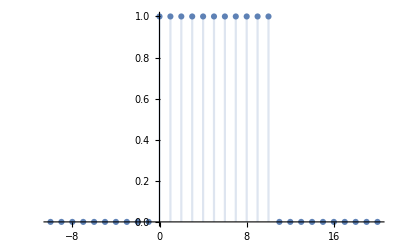

```mathematica
DiscretePlot[seg[k],{k,-10,20},PlotRange->All]
```

```mathematica
Subscript[U, seg][z_]:=ZTransform[seg[k],k,z]
```

```mathematica
Subscript[U, seg][z]
```

(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)/z^10

Ora posso riportare in z e sostituire tutto quello che ho trovato

```mathematica
Eqdifz = (ZTransform[Armak,k,z])/.{ZTransform[y[k],k,z]->Y[z],ZTransform[Subscript[u, 1][k],k,z]->Subscript[U, 1][z]}
```

Y[z]-3 (-z y[0]+z Y[z])-10 (-z^2 y[0]-z y[1]+z^2 Y[z])+24 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 Y[z])==-24 U_1[z]

Risposta

```mathematica
ris = Solve[Eqdifz,Y[z]][[1,1]][[2]]
```

(-3 z y[0]-10 z^2 y[0]+24 z^3 y[0]-10 z y[1]+24 z^2 y[1]+24 z y[2]-24 U_1[z])/(1-3 z-10 z^2+24 z^3)

```mathematica
Subscript[Y, dif][z_]:=Collect[ris,Subscript[U, 1][z]]
```

```mathematica
Subscript[Y, dif][z]
```

(-3 z y[0]-10 z^2 y[0]+24 z^3 y[0]-10 z y[1]+24 z^2 y[1]+24 z y[2])/(1-3 z-10 z^2+24 z^3)-(24 U_1[z])/(1-3 z-10 z^2+24 z^3)

Inseriamo tutto

```mathematica
Subscript[y, segnale][k_]:=Expand[InverseZTransform[Subscript[Y, dif][z]/.
{Subscript[U, 1][z]->((1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)/z^10),y[0]->Subscript[y, 100], y[1]->Subscript[y, 101],y[2]->Subscript[y, 102]},z,k]]
```

```mathematica
Subscript[y, segnale][k]
```

4793485 2^(3-2 k)-(49081 2^(1-k))/5+5624/5 (-1)^k 3^(5-k)-4793485 2^(3-2 k) UnitStep[10-k]+49081/5 2^(1-k) UnitStep[10-k]-5624/5 (-1)^k 3^(5-k) UnitStep[10-k]-(62811433 UnitStep[10-k] UnitStep[-10+k])/31850496-(5163491 UnitStep[9-k] UnitStep[-9+k])/2654208-(417505 UnitStep[8-k] UnitStep[-8+k])/221184-(32939 UnitStep[7-k] UnitStep[-7+k])/18432-(2377 UnitStep[6-k] UnitStep[-6+k])/1536-155/128 UnitStep[5-k] UnitStep[-5+k]-7/32 UnitStep[4-k] UnitStep[-4+k]+3/8 UnitStep[3-k] UnitStep[-3+k]+4 UnitStep[2-k] UnitStep[-2+k]-3 UnitStep[1-k] UnitStep[-1+k]-2 UnitStep[-k]

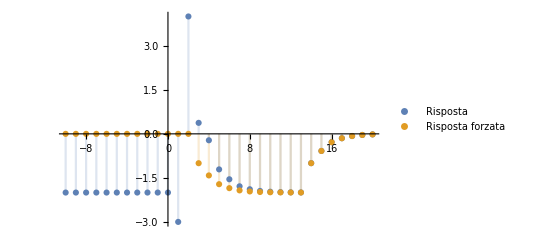

```mathematica
DiscretePlot[{4793485 2^(3-2 k)-(49081 2^(1-k))/5+5624/5 (-1)^k 3^(5-k)-4793485 2^(3-2 k) UnitStep[10-k]+49081/5 2^(1-k) UnitStep[10-k]-5624/5 (-1)^k 3^(5-k) UnitStep[10-k]-(62811433 UnitStep[10-k] UnitStep[-10+k])/31850496-(5163491 UnitStep[9-k] UnitStep[-9+k])/2654208-(417505 UnitStep[8-k] UnitStep[-8+k])/221184-(32939 UnitStep[7-k] UnitStep[-7+k])/18432-(2377 UnitStep[6-k] UnitStep[-6+k])/1536-155/128 UnitStep[5-k] UnitStep[-5+k]-7/32 UnitStep[4-k] UnitStep[-4+k]+3/8 UnitStep[3-k] UnitStep[-3+k]+4 UnitStep[2-k] UnitStep[-2+k]-3 UnitStep[1-k] UnitStep[-1+k]-2 UnitStep[-k],1/35 2^(3-2 k) 3^(1-k) (398583 (-1)^k 2^(2 k)+55924040 3^k-14329 2^(1+k) 3^k) (1-UnitStep[10-k])-(71327069 UnitStep[10-k] UnitStep[-10+k])/35831808-(5916319 UnitStep[9-k] UnitStep[-9+k])/2985984-(488309 UnitStep[8-k] UnitStep[-8+k])/248832-(39943 UnitStep[7-k] UnitStep[-7+k])/20736-(3197 UnitStep[6-k] UnitStep[-6+k])/1728-247/144 UnitStep[5-k] UnitStep[-5+k]-17/12 UnitStep[4-k] UnitStep[-4+k]-UnitStep[3-k] UnitStep[-3+k]},{k,-10,20},PlotRange->All,PlotLegends->{"Risposta", "Risposta forzata"}]
```

Verifico che la risposta libera sia uguale

```mathematica
Subscript[r, libera1] =Simplify[z C1.Inverse[z IdentityMatrix[3]-A].Subscript[x, 10]]
```

{{-(4 z (-33+13 z+12 z^2))/(1-3 z-10 z^2+24 z^3)}}

```mathematica
Subscript[r, libera2]=((-3 z y[0]-10 z^2 y[0]+24 z^3 y[0]-10 z y[1]+24 z^2 y[1]+24 z y[2])/(1-3 z-10 z^2+24 z^3))/.
{y[0]->Subscript[y, 100], y[1]->Subscript[y, 101],y[2]->Subscript[y, 102]}
```

(132 z-52 z^2-48 z^3)/(1-3 z-10 z^2+24 z^3)

```mathematica
Simplify[Subscript[r, libera2]]
```

-(4 z (-33+13 z+12 z^2))/(1-3 z-10 z^2+24 z^3)

Sono uguali

Fare anche il modello ARMA a ritardi pongo k + 3 = k’

```mathematica
Armak2 =Armaz /. {Y[z]->y[k' - 3],z Y[z]->y[k' - 2],z^2 Y[z]->y[k' - 1],z^3 Y[z]->y[k '], Subscript[U, 1][z]->Subscript[u, 1][k'-3]}
```

y[-3+k']-3 y[-2+k']-10 y[-1+k']+24 y[k']==-24 u_1[-3+k']

```mathematica
risCon = ((-3 z y[0]-10 z^2 y[0]+24 z^3 y[0]-10 z y[1]+24 z^2 y[1]+24 z y[2])/(1-3 z-10 z^2+24 z^3)-(24 Subscript[U, 1][z])/(1-3 z-10 z^2+24 z^3))/.{{y[0]->Subscript[y, 100], y[1]->Subscript[y, 101],y[2]->Subscript[y, 102]}}
```

{(132 z-52 z^2-48 z^3)/(1-3 z-10 z^2+24 z^3)-(24 U_1[z])/(1-3 z-10 z^2+24 z^3)}

```mathematica
pt = Subscript[Y, dif][z] /.
{Subscript[U, 1][z]->((1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)/z^10),y[0]->Subscript[y, 100], y[1]->Subscript[y, 101],y[2]->Subscript[y, 102]}
```

(132 z-52 z^2-48 z^3)/(1-3 z-10 z^2+24 z^3)-(24 (1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10))/(z^10 (1-3 z-10 z^2+24 z^3))

```mathematica
r[k_]:=Expand[InverseZTransform[((132 z-52 z^2-48 z^3)/(1-3 z-10 z^2+24 z^3)-(24 (1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10))/(z^10 (1-3 z-10 z^2+24 z^3))),z,k]]
```

```mathematica
r[k]
```

4793485 2^(3-2 k)-(49081 2^(1-k))/5+5624/5 (-1)^k 3^(5-k)-4793485 2^(3-2 k) UnitStep[10-k]+49081/5 2^(1-k) UnitStep[10-k]-5624/5 (-1)^k 3^(5-k) UnitStep[10-k]-(62811433 UnitStep[10-k] UnitStep[-10+k])/31850496-(5163491 UnitStep[9-k] UnitStep[-9+k])/2654208-(417505 UnitStep[8-k] UnitStep[-8+k])/221184-(32939 UnitStep[7-k] UnitStep[-7+k])/18432-(2377 UnitStep[6-k] UnitStep[-6+k])/1536-155/128 UnitStep[5-k] UnitStep[-5+k]-7/32 UnitStep[4-k] UnitStep[-4+k]+3/8 UnitStep[3-k] UnitStep[-3+k]+4 UnitStep[2-k] UnitStep[-2+k]-3 UnitStep[1-k] UnitStep[-1+k]-2 UnitStep[-k]

```mathematica
Apart[(132 z-52 z^2-48 z^3)/(1-3 z-10 z^2+24 z^3)-(24 (1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10))/(z^10 (1-3 z-10 z^2+24 z^3))]
```

-2-24/z^10-96/z^9-552/z^8-2064/z^7-9432/z^6-35712/z^5-151944/z^4-586608/z^3-2422200/z^2-9486048/z-98162/(5 (-1+2 z))-1366632/(5 (1+3 z))+38347880/(-1+4 z)

Provo a calcolare la risposta forzata

```mathematica
rispostaForzata[z_] := G[z] Subscript[U, seg][z]
```

```mathematica
rispostaForzata[z]
```

-(24 (1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10))/(z^10 (1-3 z-10 z^2+24 z^3))

```mathematica
rispostaForzatak[k_] := InverseZTransform[rispostaForzata[z],z,k]
```

```mathematica
rispostaForzatak[k]
```

1/35 2^(3-2 k) 3^(1-k) (398583 (-1)^k 2^(2 k)+55924040 3^k-14329 2^(1+k) 3^k) (1-UnitStep[10-k])-(71327069 UnitStep[10-k] UnitStep[-10+k])/35831808-(5916319 UnitStep[9-k] UnitStep[-9+k])/2985984-(488309 UnitStep[8-k] UnitStep[-8+k])/248832-(39943 UnitStep[7-k] UnitStep[-7+k])/20736-(3197 UnitStep[6-k] UnitStep[-6+k])/1728-247/144 UnitStep[5-k] UnitStep[-5+k]-17/12 UnitStep[4-k] UnitStep[-4+k]-UnitStep[3-k] UnitStep[-3+k]

Ora, prendo la risposta forzata

```mathematica
rispostaForzatak[k]
```

1/35 2^(3-2 k) 3^(1-k) (398583 (-1)^k 2^(2 k)+55924040 3^k-14329 2^(1+k) 3^k) (1-UnitStep[10-k])-(71327069 UnitStep[10-k] UnitStep[-10+k])/35831808-(5916319 UnitStep[9-k] UnitStep[-9+k])/2985984-(488309 UnitStep[8-k] UnitStep[-8+k])/248832-(39943 UnitStep[7-k] UnitStep[-7+k])/20736-(3197 UnitStep[6-k] UnitStep[-6+k])/1728-247/144 UnitStep[5-k] UnitStep[-5+k]-17/12 UnitStep[4-k] UnitStep[-4+k]-UnitStep[3-k] UnitStep[-3+k]

#### Punto7

Scrivo le mie condizioni iniziali incognite:

```mathematica
Subscript[x, inc]= {{Subscript[x, 011]},{Subscript[x, 021]},{Subscript[x, 031]}}
```

{{x_11},{x_21},{x_31}}

```mathematica
Subscript[x, inc]//MatrixForm
```

(x_11
x_21
x_31)

```mathematica
ZTransform[UnitStep[k],k,z]
```

z/(-1+z)

Calcolo y[0],y[1],y[2]

```mathematica
Subscript[y, 1111]= (C1.Subscript[x, inc])[[1,1]]
```

x_21-x_31

```mathematica
Subscript[y, 1112]= (C1.A.Subscript[x, inc])[[1,1]]
```

x_11+x_21+x_31

```mathematica
Subscript[y, 1113]= (C1.A.A.Subscript[x, inc])[[1,1]]
```

-x_11+x_31

```mathematica
Eq = (ZTransform[Armak,k,z])/.{ZTransform[y[k],k,z]->Y[z],ZTransform[Subscript[u, 1][k],k,z]->Subscript[U, 1][z]}
```

Y[z]-3 (-z y[0]+z Y[z])-10 (-z^2 y[0]-z y[1]+z^2 Y[z])+24 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 Y[z])==-24 U_1[z]

```mathematica
ri = Solve[Eqdifz,Y[z]][[1,1]][[2]]
```

(-3 z y[0]-10 z^2 y[0]+24 z^3 y[0]-10 z y[1]+24 z^2 y[1]+24 z y[2]-24 U_1[z])/(1-3 z-10 z^2+24 z^3)

```mathematica
Subscript[Y, gr][z_]:=Collect[ri,Subscript[U, 1][z]]
```

```mathematica
Subscript[Y, gr][z_]
```

(-3 z y[0]-10 z^2 y[0]+24 z^3 y[0]-10 z y[1]+24 z^2 y[1]+24 z y[2])/(1-3 z-10 z^2+24 z^3)-(24 U_1[z])/(1-3 z-10 z^2+24 z^3)

```mathematica
Subscript[y, g][k_]:=Expand[InverseZTransform[Subscript[Y, gr][z]/.
{Subscript[U, 1][z]->(z/(-1+z)),y[0]->Subscript[y, 1111], y[1]->Subscript[y, 1112],y[2]->Subscript[y, 1113]},z,k]]
```

```mathematica
Subscript[y, g][k][[1,1]]
```

-2+(3 2^(4-k))/5+2/35 (-1)^k 3^(3-k)-4^(3-k)/7+2^(3-2 k) x_11-11/5 2^(1-k) x_11-2/5 (-1)^k 3^(2-k) x_11-1/7 (-1)^k 3^(2-k) x_21+1/7 4^(2-k) x_21+7/5 2^(2-k) x_31+1/35 (-1)^k 3^(2-k) x_31-3/7 4^(2-k) x_31

```mathematica
Subscript[y, fo][k_]:=Expand[InverseZTransform[(-(24 Subscript[U, 1][z])/(1-3 z-10 z^2+24 z^3))/.{Subscript[U, 1][z]->(z/(-1+z))},z,k]]
```

```mathematica
Subscript[y, fo][k]
```

-2-1/7 2^(6-2 k)+(3 2^(4-k))/5+2/35 (-1)^k 3^(3-k)

```mathematica
Subscript[y, lib]=Simplify[((-3 z y[0]-10 z^2 y[0]+24 z^3 y[0]-10 z y[1]+24 z^2 y[1]+24 z y[2])/(1-3 z-10 z^2+24 z^3))/.{y[0]->Subscript[y, 1111], y[1]->Subscript[y, 1112],y[2]->Subscript[y, 1113]}][[1,1]]
```

(z ((-34+24 z) x_11+(-13+14 z+24 z^2) x_21+(17+34 z-24 z^2) x_31))/(1-3 z-10 z^2+24 z^3)

```mathematica
Subscript[y, reg][z_] := ZTransform[-2,k,z]
```

```mathematica
Subscript[y, reg][z]
```

-(2 z)/(-1+z)

```mathematica
Subscript[y, tranz][z_]:=ZTransform[((3 2^(4-k))/5+2/35 (-1)^k 3^(3-k)-4^(3-k)/7+2^(3-2 k) -11/5 2^(1-k)-2/5 (-1)^k 3-1/7 (-1)^k 3^(2-k) Subscript[x, 21]+1/7 4^(2-k) Subscript[x, 21]+7/5 2^(2-k) Subscript[x, 31]+1/35 (-1)^k 3^(2-k) Subscript[x, 31]-3/7 4^(2-k) Subscript[x, 31]),k,z]
```

```mathematica
Subscript[y, tranz][z]
```

(z (22+28 z+48 z^2+(-34+24 z) x_11+(-13+14 z+24 z^2) x_21+17 x_31+34 z x_31-24 z^2 x_31))/((-1+2 z) (1+3 z) (-1+4 z))

```mathematica
for = -(24 Subscript[U, 1][z])/(1-3 z-10 z^2+24 z^3)/.
{Subscript[U, 1][z]->(z/(-1+z))}
```

-(24 z)/((-1+z) (1-3 z-10 z^2+24 z^3))

```mathematica
Expand[(-1+z) (1-3 z-10 z^2+24 z^3)]
```

-1+4 z+7 z^2-34 z^3+24 z^4

```mathematica
Subscript[y, fo][z_]:=ZTransform[(-2-1/7 2^(6-2 k)+(3 2^(4-k))/5+2/35 (-1)^k 3^(3-k)),k,z]
```

```mathematica
Subscript[y, fo][z]
```

-(24 z)/(-1+4 z+7 z^2-34 z^3+24 z^4)

```mathematica
trans =Expand[fo - Subscript[y, reg][z]]
```

(2 z)/(-1+z)-(24 z)/((-1+z) (1-3 z-10 z^2+24 z^3))

```mathematica
Numerator[Simplify[Expand[Subscript[y, lib]+trans]]]
```

z (22+28 z+48 z^2+(-34+24 z) x_11+(-13+14 z+24 z^2) x_21+17 x_31+34 z x_31-24 z^2 x_31)

```mathematica
CoefficientList[Numerator[Simplify[Expand[Subscript[y, lib]+trans]]],z]
```

{0,22-34 x_11-13 x_21+17 x_31,28+24 x_11+14 x_21+34 x_31,48+24 x_21-24 x_31}

```mathematica
Solve[CoefficientList[Numerator[Simplify[Expand[Subscript[y, lib]+trans]]],z] == {0,0,0,0},{Subscript[x, 11],Subscript[x, 21],Subscript[x, 31]}]
```

{{x_11→4/3,x_21→-8/3,x_31→-2/3}}

```mathematica
Σ = StateSpaceModel[{A,B,C1}]
```

-17/36-7/18-7/182/317/7225/3643/36-1/3-55/72-11/367/36-1/301-10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Subscript[x, bu] = {{4/3},{-8/3},{-2/3}}
```

{{4/3},{-8/3},{-2/3}}

```mathematica
Subscript[y, conf1]= (C1.Subscript[x, bu])[[1,1]]
```

-2

```mathematica
Subscript[y, conf2]= (C1.A.Subscript[x, bu])[[1,1]]
```

-2

```mathematica
Subscript[y, conf3]= (C1.A.A.Subscript[x, bu])[[1,1]]
```

-2

```mathematica
Subscript[y, conferma][k_]:=Expand[InverseZTransform[Subscript[Y, gr][z]/.
{Subscript[U, 1][z]->(z/(-1+z)),y[0]->Subscript[y, conf1], y[1]->Subscript[y, conf2],y[2]->Subscript[y, conf3]},z,k]]
```

```mathematica
Subscript[y, conferma][k]
```

-2